# CS 298 - Lab 8

## Kyle Perra - 7/28/15

## Functions Without Antiderivatives

```mathematica
Clear[f,x,z]
f[x_]:=(Cos[x]^2+1)^0.5
Integrate[f[x],{x,0,2}]
```

(1.9101-0.711959 ⅈ)+(0.+0.299509 ⅈ) AppellF1[1.5,0.5,0.5,2.5,1.17317818956819,0.586589094784097]

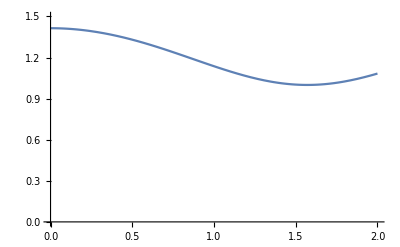

```mathematica
Plot[f[x],{x,0,2},PlotRange->{{0.0,2.0},{0,1.5}}]
```

## Monte Carlo - First Attempt

```mathematica
dartTBl=Table[If[Random[Real,{0,1.5}]<f[Random[Real,{0,2}]],1,0],{10}]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
fractionUnder=Count[dartTBl,1]/10
```

1

```mathematica
rectArea=(2-0)*1.5
```

3.

```mathematica
area=fractionUnder*rectArea
```

3.

## Monte Carlo - Second Attempt

```mathematica
dartTB2 = Table[If[Random[Real,{0,1.5}]<f[Random[Real,{0,2}]],1,0],{50}]
```

{1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,0,0,1,0,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
fractionUnder=Count[dartTB2,1]/50
```

22/25

```mathematica
rectArea=(2-0)*1.5
```

3.

```mathematica
area = fractionUnder*rectArea
```

2.64